```mathematica
ClearAll["Global`*"]
```

Simplify with 2 prey

```mathematica
VarTablefunc[{prey1_,prey2_,diff_}] := (
VarZTable=Table[
mu = {-15,-15+diff,-15};
sig = {0.8,1.2,1};
nprey = Length[mu];
Dparam =Table[1,{nprey}];
Dparam[[prey1]] = a;
Dparam[[prey2]] = a;

a0 = Total[Dparam];
VarZ=N[Sum[Dparam[[i]]/a0(sig[[i]]^2+mu[[i]]^2) - (Dparam[[i]]^2 *mu[[i]]^2)/a0^2,{i,1,nprey}] - Sum[(Dparam[[i]]*Dparam[[j]]*mu[[i]]*mu[[j]])/a0^2 Boole[i≠j],{i,1,nprey},{j,1,nprey}]];
propi = a/a0;
{propi,VarZ},
{a,1,1000,1}];
VarXTable = Table[{VarZTable[[i]][[1]],(λ*VarZTable[[i]][[2]])/2},{λ,0,1,0.1},{i,1,Length[VarZTable]}];
Return[{VarZTable,VarXTable}];
)
```

{A (Dotted),-15,0.8}

{B (Dashed),-15,1.2}

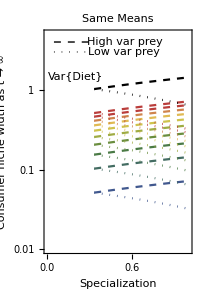

```mathematica
prey1 = 1;
prey2 = 2;
diff = 0;
VarA = VarTablefunc[{prey1,prey1,diff}];VarZTableA = VarA[[1]];VarXTableA = VarA[[2]];
VarB = VarTablefunc[{prey2,prey2,diff}];VarZTableB = VarB[[1]];VarXTableB = VarB[[2]];
{"A (Dotted)",mu[[prey1]],sig[[prey1]]}
{"B (Dashed)",mu[[prey2]],sig[[prey2]]}

VarDiff0=Show[{

ListLogPlot[VarZTableB,PlotStyle->Directive[{Black,Dashed}],PlotRange->{{0,1},{0.01,5}},Joined->True,AspectRatio->1.5,FrameLabel->{"Specialization","Consumer niche width as t → ∞"},Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},Epilog->Style[Text["Var{Diet}",{0.2,Log@1.5}],12],PlotLabel->"Same Means"],
Table[
ListLogPlot[VarXTableB[[i+1]],PlotRange->All,Frame->True,PlotLabel->"Var{X}",PlotStyle->Directive[Dashed,ColorData["DarkRainbow",i/10]],Joined->True],{i,1,10,1}],

ListLogPlot[VarZTableA,PlotStyle->Directive[{Black,Dotted}],PlotRange->{{0,1},{0.01,5}},Joined->True,Epilog->Style[Text["Var{Z}",{0.15,Log@0.3}],12]],
Table[
ListLogPlot[VarXTableA[[i+1]],PlotRange->All,Frame->True,PlotLabel->"Var{X}",PlotStyle->Directive[Dotted,ColorData["DarkRainbow",i/10]],Joined->True],{i,1,10,1}],

Graphics[{Thick,Dashed,Line[{{0.05,Log@4},{0.3,Log@4}}]}],
Graphics[{Thick,Dotted,Line[{{0.05,Log@3},{0.3,Log@3}}]}],

Graphics[Text[Style["High var prey"],{0.55,Log@4}]],
Graphics[Text["Low var prey",{0.54,Log@3}]]

},ImageSize->200]
```

{A (Dotted),-15,0.8}

{B (Dashed),-5,1.2}

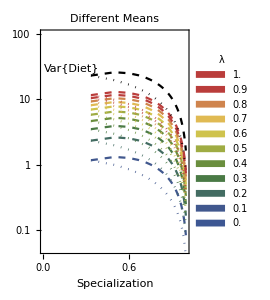

```mathematica
prey1 = 1;
prey2 = 2;
diff = 10;
VarA = VarTablefunc[{prey1,prey1,diff}];VarZTableA = VarA[[1]];VarXTableA = VarA[[2]];
VarB = VarTablefunc[{prey2,prey2,diff}];VarZTableB = VarB[[1]];VarXTableB = VarB[[2]];
{"A (Dotted)",mu[[prey1]],sig[[prey1]]}
{"B (Dashed)",mu[[prey2]],sig[[prey2]]}

VarDiff10=Show[{

ListLogPlot[VarZTableB,PlotStyle->Directive[{Black,Dashed}],PlotRange->{{0,1},{0.05,100}},Joined->True,AspectRatio->1.5,FrameLabel->{"Specialization",""},Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},Epilog->Style[Text["Var{Diet}",{0.2,Log@30}],12],PlotLabel->"Different Means"],
Table[
ListLogPlot[VarXTableB[[i+1]],PlotRange->All,Frame->True,PlotLabel->"Var{X}",PlotStyle->Directive[Dashed,ColorData["DarkRainbow",i/10]],Joined->True],{i,1,10,1}],

ListLogPlot[VarZTableA,PlotStyle->Directive[{Black,Dotted}],PlotRange->{{0,1},{0.05,100}},Joined->True,Epilog->Style[Text["Var{Z}",{0.15,Log@0.3}],12],PlotLegends->SwatchLegend["DarkRainbow",Table[λ,{λ,0,1,0.1}],LegendLabel->"λ",LegendFunction->None,LegendMargins->1,LegendLayout->{"ReversedColumn",1}]],
Table[
ListLogPlot[VarXTableA[[i+1]],PlotRange->All,Frame->True,PlotLabel->"Var{X}",PlotStyle->Directive[Dotted,ColorData["DarkRainbow",i/10]],Joined->True],{i,1,10,1}](*,
SwatchLegend["DarkRainbow",Table[λ,{λ,0,1,0.1}],LegendLabel->"λ",LegendFunction->None,LegendMargins->1,LegendLayout->{"ReversedColumn",1}]
*)
(*Graphics[{Thick,Dashed,Line[{{0.05,Log@80},{0.3,Log@80}}]}],
Graphics[{Thick,Dotted,Line[{{0.05,Log@50},{0.3,Log@50}}]}],

Graphics[Text[Style["High var prey"],{0.55,Log@80}]],
Graphics[Text["Low var prey",{0.54,Log@50}]]*)

},ImageSize->200]
```

```mathematica
VarPlot = Row[{
VarDiff0,
VarDiff10},""]
```

-Graphics--Graphics-

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_static.pdf",VarPlot]
```

/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_static.pdf